## Codes for generating the PCA figures

```mathematica
SeedRandom[1234];
```

```mathematica
PlotterAdjuster[plot_]:=Show[plot,PlotLabel->None,LabelStyle->{36,GrayLevel[0]},AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[3]],Method->{"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
MaxSVDValue=15;
```

```mathematica
MaxTrainingPoints=40;
```

```mathematica
LHCMatrixRandomizer[nmax_]:=Module[{},

TrainingNumberHL=nmax;
MatrixLH=Table[i,{i,1,TrainingNumberHL},{j,1,2}];
For[i=1,i<=TrainingNumberHL,i++,

Indexval=RandomInteger[{1,TrainingNumberHL}];
MatVal1=MatrixLH[[i]][[2]];
MatVal2=MatrixLH[[Indexval]][[2]];
MatrixLH[[i]][[2]]=MatVal2;
MatrixLH[[Indexval]][[2]]=MatVal1


];
MatrixLH
]
```

```mathematica
LHCMatrix=LHCMatrixRandomizer[MaxTrainingPoints]
```

{{1,7},{2,3},{3,27},{4,38},{5,16},{6,26},{7,19},{8,40},{9,12},{10,20},{11,1},{12,31},{13,9},{14,25},{15,29},{16,17},{17,10},{18,34},{19,8},{20,14},{21,30},{22,21},{23,4},{24,15},{25,32},{26,11},{27,23},{28,24},{29,13},{30,2},{31,18},{32,5},{33,22},{34,33},{35,36},{36,37},{37,28},{38,39},{39,35},{40,6}}

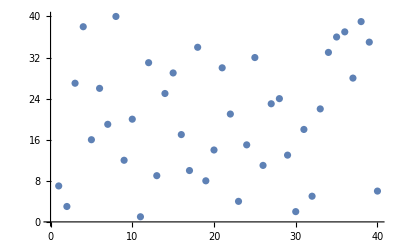

```mathematica
ListPlot[LHCMatrix]
```

## Gross-P equation

### Initializing global parameters:

```mathematica
Xmin=-10;                                    (* Lower limit range for the function *)
Xmax=10;                                      (* Upper limit range for the function *)
dx=0.02;                                       (*Step size for the finite element method*)
x=Range[Xmin,Xmax,dx]; (*Initialize the abcissa*)
len=Length[x];     (*Initialize the lengeth of solution vector*)

(*Laplacian matrix for the discrete system*)
lap=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{len,len}]/dx^2;
```

### Variable initialization:

#### Placeholders for the high-fidelity solution of the differential equation

```mathematica
phi=Array[phiVal,len];(* Placeholder for a particular eigenfunction we are calculating *)
lam;(* Placeholder for a particular eigenvalue we are calculating *)
```

```mathematica
eigEq[q_,k_]:=(Dot[-lap,phi]+k*(x^2)*phi+q*phi^3==lam*phi);(*Eigenvalue equation*)
normEq[q_,k_]:=Dot[phi,phi]==1.0/dx;(*Normalization condition*)

eqns[q_,k_]:=Append[Thread[eigEq[q,k]],normEq[q,k]]; (*Full (N+1) equation set*)
```

### Finding the (High-Fidelity) lowest energy solution:

We utilize FindRoot to find the solution to the eigenvalue equation. We use an eigenfunction of the harmonic oscillator, or a constant function, as an initial guess to speed up calculations. FindRoot helps us to bypass finding all of the other eigenfunctions we don’t care about by starting near the basin of attraction of the first eigenmode.

```mathematica
(*Some times the exact solver converges to the wrong excited state, we use Guess Lam and GuessInvSigma to give something that is closer to it*)
```

```mathematica
GuessLamb[q_,k_]=Sqrt[k]+Sqrt[q];
```

```mathematica
GuessInvSigma[q_,k_]=Sqrt[k]/(1+Sqrt[q]);
```

```mathematica
sol[q_,k_]:=FindRoot[eqns[q,k],Transpose[{Prepend[phi,lam],Prepend[Exp[-x^2*(GuessInvSigma[q,k])/2]/(Pi/(GuessInvSigma[q,k]))^(1/4),(GuessLamb[q,k])]}],PrecisionGoal->10]; (*Solution routine for the full set of (N+1) equations, as a function of q and k*)
```

```mathematica
KLimits={5,30};
QLimits={0,30};
```

```mathematica
TraininPointsMakerGP[Matrixlh_]:=Module[{},
TrainingNumberHL=Length[Matrixlh];
TP={};

TotalPoints=TrainingNumberHL;
For[ik=1,ik<=TotalPoints,ik++,


AppendTo[TP,{(Matrixlh[[ik]][[1]])*(QLimits[[2]]-QLimits[[1]])/(TrainingNumberHL+1)+QLimits[[1]],(Matrixlh[[ik]][[2]])*(KLimits[[2]]-KLimits[[1]])/(TrainingNumberHL+1)+KLimits[[1]]}]




];

TP
]
```

```mathematica
N[TraininPointsMakerGP[LHCMatrix]]
```

{{0.731707,9.26829},{1.46341,6.82927},{2.19512,21.4634},{2.92683,28.1707},{3.65854,14.7561},{4.39024,20.8537},{5.12195,16.5854},{5.85366,29.3902},{6.58537,12.3171},{7.31707,17.1951},{8.04878,5.60976},{8.78049,23.9024},{9.5122,10.4878},{10.2439,20.2439},{10.9756,22.6829},{11.7073,15.3659},{12.439,11.0976},{13.1707,25.7317},{13.9024,9.87805},{14.6341,13.5366},{15.3659,23.2927},{16.0976,17.8049},{16.8293,7.43902},{17.561,14.1463},{18.2927,24.5122},{19.0244,11.7073},{19.7561,19.0244},{20.4878,19.6341},{21.2195,12.9268},{21.9512,6.21951},{22.6829,15.9756},{23.4146,8.04878},{24.1463,18.4146},{24.878,25.122},{25.6098,26.9512},{26.3415,27.561},{27.0732,22.0732},{27.8049,28.7805},{28.5366,26.3415},{29.2683,8.65854}}

```mathematica
BasisConstruction[TrainPoints_]:=Module[{},


numTrain=Length[TrainPoints];
listPhi=Array[trainPhi,{numTrain,len}]; (*List of the training functions 'phi'*)

For[i=1,i≤numTrain,i++,
placeholderSol=sol[TrainPoints[[i]][[1]],TrainPoints[[i]][[2]]];(*dummy variable for substitution*)
listPhi[[i]]=phi/.placeholderSol;

];

listPhi

]
```

```mathematica
{uGP, σGP, vGP}=SingularValueDecomposition[BasisConstruction[TraininPointsMakerGP[LHCMatrix]]]
```

{{1},{1},{{2.0205×10^-16,7.47729×10^-17,9.39148×10^-16,-6.65369×10^-15,8.96619×10^-16,6.05579×10^-14,7.40329×10^-14,2.16509×10^-13,3.26701×10^-12,1.31962×10^-11,1.97346×10^-11,1.55403×10^-11,977,2.26819×10^-24,2.00741×10^-24,1.77086×10^-24,1.55466×10^-24,1.35512×10^-24,1.16868×10^-24,9.91984×10^-25,8.21952×10^-25,6.55905×10^-25,4.91728×10^-25,3.28011×10^-25,1.64107×10^-25},999,{1}}}
 |  |  |  |

```mathematica
SVDValsGP=Table[σGP[[i]][[i]]/σGP[[1]][[1]],{i,1,MaxSVDValue}]
```

{1.,0.151669,0.0475263,0.0111521,0.00346466,0.000987632,0.000386593,0.0000979645,0.0000261418,6.38185×10^-6,3.52778×10^-6,9.78755×10^-7,4.33763×10^-7,1.46656×10^-7,5.84901×10^-8}

```mathematica
listPhiGPPlot=BasisConstruction[TraininPointsMakerGP[LHCMatrix]];
```

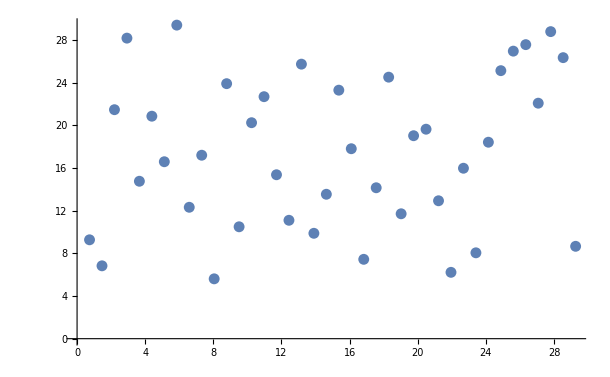

```mathematica
ListPlot[TraininPointsMakerGP[LHCMatrix]]
```

```mathematica
listPhiGPPlotX=Table[{x[[j]],listPhiGPPlot[[i*4]][[j]]},{i,1,10},{j,1,Length[x]}];
```

```mathematica
(*listPhiGPPlotX=Table[{x[[j]],listPhiGPPlot[[i]][[j]]},{i,1,Length[listPhiGPPlot]},{j,1,Length[x]}];*)
```

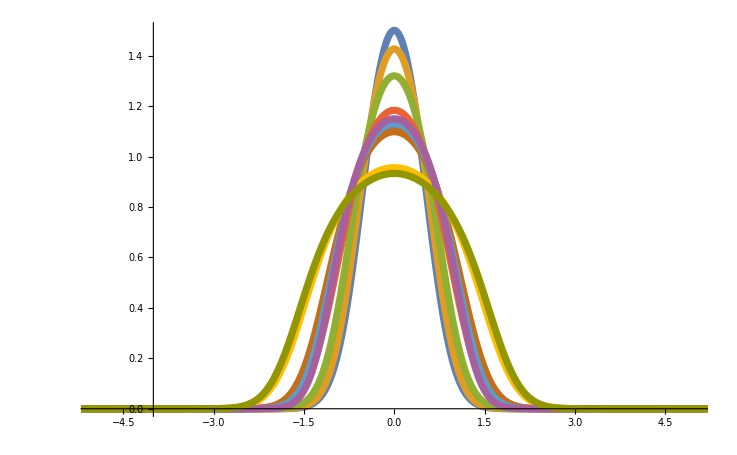

```mathematica
PlotGP=ListPlot[listPhiGPPlotX,Joined->True,PlotStyle->{Thickness[0.007]},AxesOrigin->{-4,0},PlotRange->{{-5,5},All}]
```

```mathematica
listPhiGPSVDPlotX=Table[{x[[j]],1/Sqrt[dx]*Transpose[vGP][[i]][[j]]},{i,1,4},{j,1,Length[x]}];
```

```mathematica
listPhiGPSVDPlotX2={Transpose[{Transpose[listPhiGPSVDPlotX[[1]]][[1]],-Transpose[listPhiGPSVDPlotX[[1]]][[2]]}],listPhiGPSVDPlotX[[2]],listPhiGPSVDPlotX[[3]],listPhiGPSVDPlotX[[4]]};
```

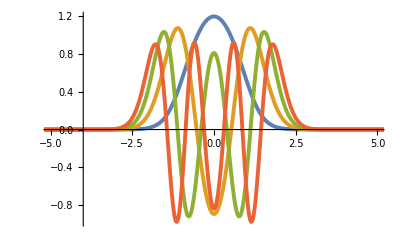

```mathematica
PlotGPSVD=ListPlot[listPhiGPSVDPlotX2,Joined->True,PlotStyle->{Thickness[0.007]},AxesOrigin->{-4,0},PlotRange->{{-5,5},All}]
```

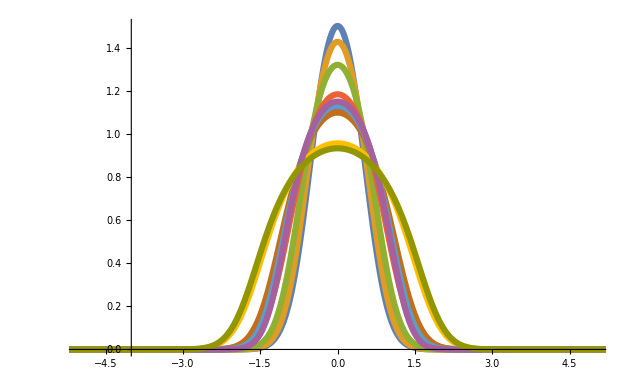

```mathematica
PlotterAdjuster[PlotGP]
```

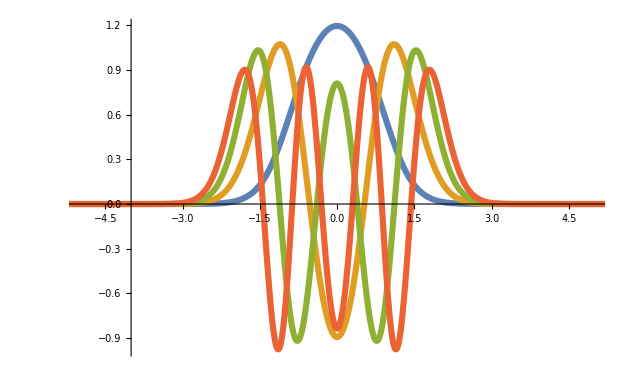

```mathematica
PlotterAdjuster[PlotGPSVD]
```

## Wandering well Equation

```mathematica
MaxTrainingPoints
```

40

```mathematica
x0Vals=Table[RandomReal[{-5,5}],{i,1,MaxTrainingPoints}]
```

{1.85697,-1.88131,2.09733,-4.82607,-1.94612,-0.942028,2.72804,0.917864,4.28085,2.16811,-0.573154,4.25846,0.586618,-2.76104,-4.03628,0.49183,3.88034,3.82079,-2.03051,0.18834,4.72651,1.55332,-4.67122,-3.49616,-1.76425,3.77425,1.15228,3.16842,0.37191,-0.856979,2.22149,-0.684648,2.29056,0.370665,1.31428,1.37473,-2.41099,-1.51333,2.02907,-0.1241}

```mathematica
x0Valsplot=Table[{x0Vals[[i]],0},{i,1,Length[x0Vals]}]
```

{{1.85697,0},{-1.88131,0},{2.09733,0},{-4.82607,0},{-1.94612,0},{-0.942028,0},{2.72804,0},{0.917864,0},{4.28085,0},{2.16811,0},{-0.573154,0},{4.25846,0},{0.586618,0},{-2.76104,0},{-4.03628,0},{0.49183,0},{3.88034,0},{3.82079,0},{-2.03051,0},{0.18834,0},{4.72651,0},{1.55332,0},{-4.67122,0},{-3.49616,0},{-1.76425,0},{3.77425,0},{1.15228,0},{3.16842,0},{0.37191,0},{-0.856979,0},{2.22149,0},{-0.684648,0},{2.29056,0},{0.370665,0},{1.31428,0},{1.37473,0},{-2.41099,0},{-1.51333,0},{2.02907,0},{-0.1241,0}}

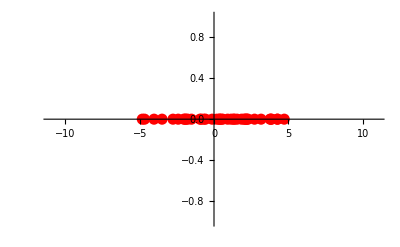

```mathematica
ListPlot[x0Valsplot,PlotStyle->{PointSize[0.02],Red},PlotRange->{{-11,11},{-1,1}}]
```

```mathematica
SinFunc[x0_,xxx_]:=Module[{val},
If[xxx-x0≥0&&xxx-x0≤1,
Sin[(xxx-x0)*Pi],
0]


]
```

```mathematica
listPhiSine=Table[SinFunc[x0Vals[[i]],j],{i,1,Length[x0Vals]},{j,-12,12,0.01}];
```

```mathematica
XXWell=Table[j,{j,-12,12,0.01}];
```

```mathematica
{uS, σS, vS} = SingularValueDecomposition[listPhiSine,MaxSVDValue];
```

```mathematica
SVDValsSin=Table[σS[[i]][[i]]/σS[[1]][[1]],{i,1,Length[σS]}]
```

{1.,0.932583,0.877654,0.820504,0.81858,0.797394,0.594932,0.560805,0.543873,0.532442,0.504846,0.480786,0.443265,0.404685,0.370014}

```mathematica
listPhiSinePlot=Table[{j,Sqrt[2]*SinFunc[x0Vals[[i]],j]},{i,1,Length[x0Vals]},{j,-12,12,0.01}];
```

```mathematica
listPhiSineSVDPlot=Table[{XXWell[[j]],1/Sqrt[0.01]Transpose[vS][[i]][[j]]},{i,1,4},{j,1,Length[XXWell]}];
```

```mathematica
listPhiSineSVDPlot2={listPhiSineSVDPlot[[1]],listPhiSineSVDPlot[[2]],Transpose[{Transpose[listPhiSineSVDPlot[[3]]][[1]],-Transpose[listPhiSineSVDPlot[[3]]][[2]]}],listPhiSineSVDPlot[[4]]};
```

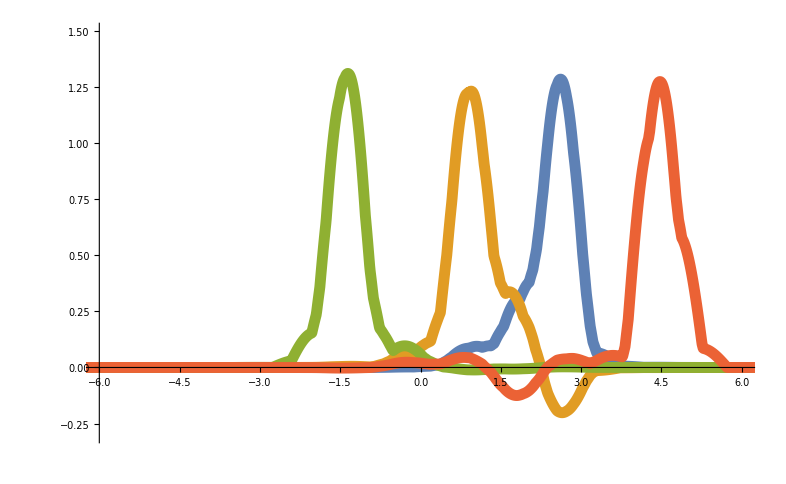

```mathematica
PlotSineSVD=ListPlot[listPhiSineSVDPlot2,Joined->True,PlotRange->{{-6,6},{-0.3,1.5}},PlotStyle->{Thickness[0.01]},AxesOrigin->{-6,0},Ticks->{0,0.5,1}]
```

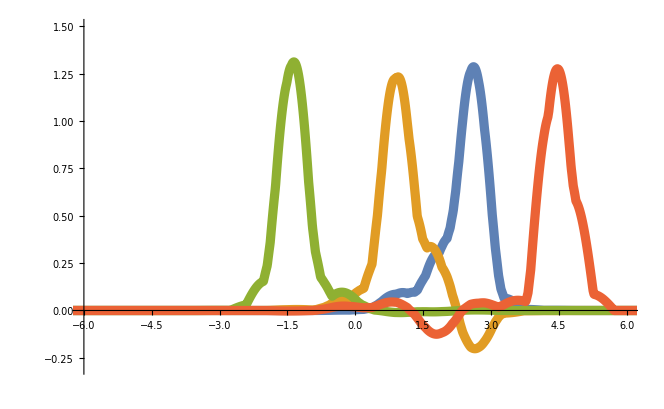

```mathematica
PlotterAdjuster[PlotSineSVD]
```

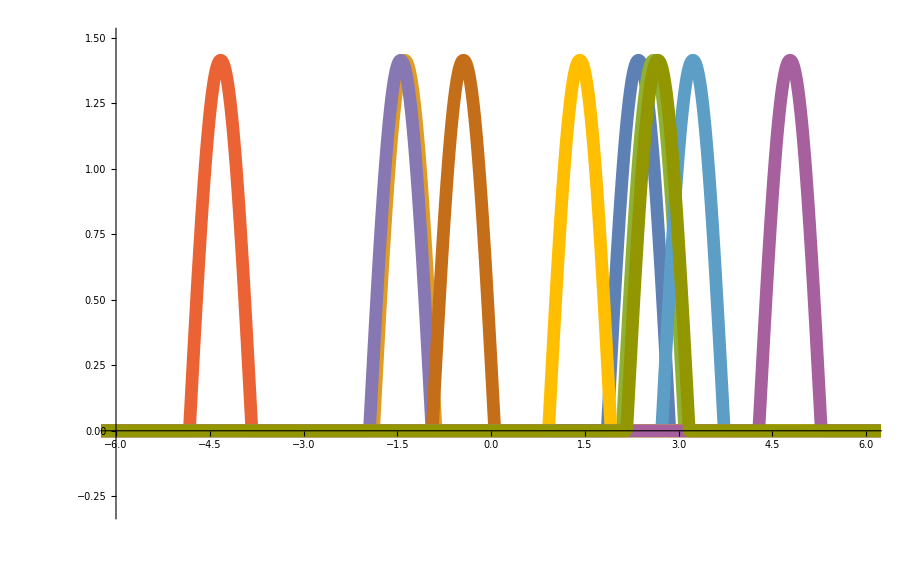

```mathematica
PlotSine=ListPlot[listPhiSinePlot[[1;;10]],Joined->True,PlotRange->{{-6,6},{-0.3,1.5}},PlotStyle->{Thickness[0.01]},AxesOrigin->{-6,0},Ticks->{Automatic,Automatic}]
```

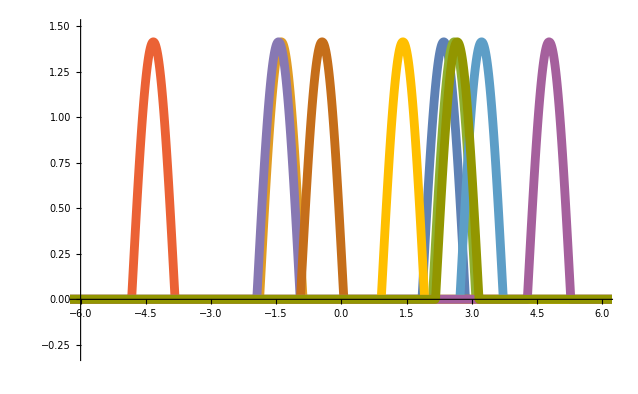

```mathematica
PlotterAdjuster[PlotSine]
```

## Scattering Part

```mathematica
XMax=40;
dx=0.01;
xList=Range[0,XMax,dx];
```

```mathematica
V[r_,V0R_,V0S_,p_]=(V0R*Exp[-1.487*(r/p)^2]+V0S*Exp[-0.465*(r/p)^2])1/p^2
```

(ⅇ^(-(1.487 r^2)/p^2) V0R+ⅇ^(-(0.465 r^2)/p^2) V0S)/p^2

```mathematica
hbarc=1;
```

```mathematica
mu=hbarc^2/41.47105/2;
```

```mathematica
EqSolver[V0R_,V0S_,p_]:=NDSolve[{-PHI''[XX]+(V[XX,V0R,V0S,p]*2mu/hbarc^2-1)*PHI[XX]==0,PHI[0]==0,PHI'[0]==1},PHI,{XX,0,3*XMax},MaxStepSize->0.001](*Added the factor of 3 to XMax because otherwise with the change of variables the function had to extrapolate*)
```

```mathematica
TruePhiSolver[V0R_,V0S_,p_]:=Module[{Func,TauTau,AA},

Func=PHI/.EqSolver[V0R,V0S,p][[1]];


Table[Func[xList[[XXi]]],{XXi,1,Length[xList]}]



]
```

```mathematica
V0RLimits={100,300};
V0SLimits={-200,0};
```

```mathematica
TraininPointsMakerScatt[Matrixlh_]:=Module[{},
TrainingNumberHL=Length[Matrixlh];
TP={};

TotalPoints=TrainingNumberHL;
For[ik=1,ik<=TotalPoints,ik++,


AppendTo[TP,{(Matrixlh[[ik]][[1]])*(V0RLimits[[2]]-V0RLimits[[1]])/(TrainingNumberHL+1)+V0RLimits[[1]],(Matrixlh[[ik]][[2]])*(V0SLimits[[2]]-V0SLimits[[1]])/(TrainingNumberHL+1)+V0SLimits[[1]]}]




];

TP
]
```

```mathematica
TraininPointsMakerScatt[LHCMatrix]
```

{{4300/41,-6800/41},{4500/41,-7600/41},{4700/41,-2800/41},{4900/41,-600/41},{5100/41,-5000/41},{5300/41,-3000/41},{5500/41,-4400/41},{5700/41,-200/41},{5900/41,-5800/41},{6100/41,-4200/41},{6300/41,-8000/41},{6500/41,-2000/41},{6700/41,-6400/41},{6900/41,-3200/41},{7100/41,-2400/41},{7300/41,-4800/41},{7500/41,-6200/41},{7700/41,-1400/41},{7900/41,-6600/41},{8100/41,-5400/41},{8300/41,-2200/41},{8500/41,-4000/41},{8700/41,-7400/41},{8900/41,-5200/41},{9100/41,-1800/41},{9300/41,-6000/41},{9500/41,-3600/41},{9700/41,-3400/41},{9900/41,-5600/41},{10100/41,-7800/41},{10300/41,-4600/41},{10500/41,-7200/41},{10700/41,-3800/41},{10900/41,-1600/41},{11100/41,-1000/41},{11300/41,-800/41},{11500/41,-2600/41},{11700/41,-400/41},{11900/41,-1200/41},{12100/41,-7000/41}}

```mathematica
Length[LHCMatrix]
```

40

## PCA Analysis for a fixed energy

```mathematica
Enn=50;
```

```mathematica
TPSc=TraininPointsMakerScatt[LHCMatrix];
```

```mathematica
TrainingPointsScattEn50=Table[{TPSc[[i]][[1]],TPSc[[i]][[2]],Sqrt[Enn*2*mu]},{i,1,Length[TPSc]}];
```

```mathematica
BasisConstructionScatt[TrainPoints_]:=Module[{},


numTrain=Length[TrainPoints];
listPhi={};

For[i=1,i≤numTrain,i++,
placeholderSol=TruePhiSolver[TrainPoints[[i]][[1]],TrainPoints[[i]][[2]],TrainPoints[[i]][[3]]];(*dummy variable for substitution*)
AppendTo[listPhi,placeholderSol];

];

listPhi

]
```

```mathematica
ScatFuncsForPlotEn50=BasisConstructionScatt[TrainingPointsScattEn50];
```

```mathematica
SolsDisplayVaryEn50=Table[{xList[[i]],ScatFuncsForPlotEn50[[j*4]][[i]]},{j,1,10},{i,1,1500}];
```

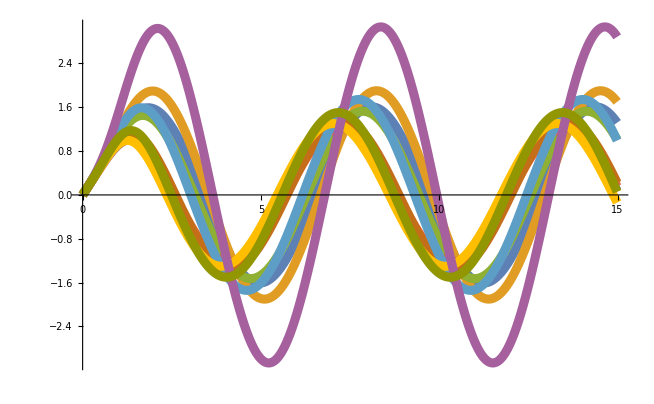

```mathematica
PlotScattEn50=ListPlot[SolsDisplayVaryEn50,Joined->True,PlotStyle->{Thickness[0.01]},Ticks->{{0,5,10,15},Automatic}]
```

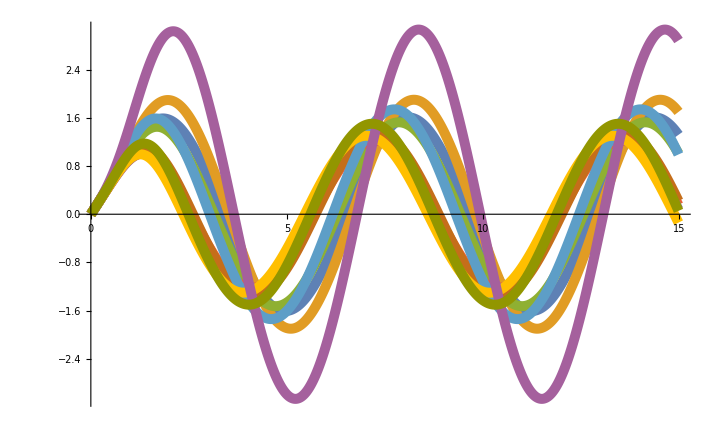

```mathematica
PlotterAdjuster[PlotScattEn50]
```

```mathematica
listPhiScattE50=BasisConstructionScatt[TrainingPointsScattEn50];
```

```mathematica
{uSca50, σSca50, vSca50} = SingularValueDecomposition[listPhiScattE50,MaxSVDValue];
```

```mathematica
SVDValsSca50=Table[σSca50[[i]][[i]]/σSca50[[1]][[1]],{i,1,Length[σSca50]}]
```

{1.,0.501027,0.0142033,0.00258844,0.000183168,0.0000173313,1.65285×10^-6,1.06313×10^-7,3.76145×10^-8,2.73401×10^-9,2.77957×10^-10,1.64818×10^-11,2.35642×10^-12,1.20269×10^-12,9.92504×10^-14}

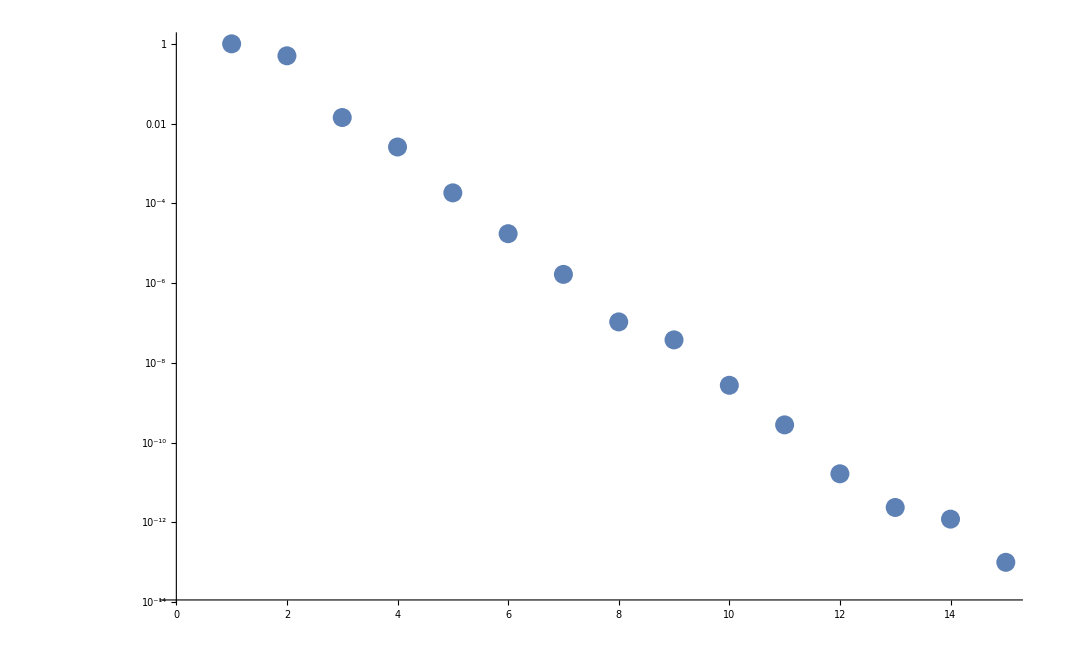

```mathematica
ListLogPlot[SVDValsSca50]
```

```mathematica
listPhiScattEn50SVDPlot=Table[{xList[[j]],10*Transpose[vSca50][[i]][[j]]},{i,1,4},{j,1,Length[xList]}];
```

```mathematica
listPhiScattEn50SVDPlot2={Transpose[{Transpose[listPhiScattEn50SVDPlot[[1]]][[1]],-Transpose[listPhiScattEn50SVDPlot[[1]]][[2]]}],listPhiScattEn50SVDPlot[[2]],listPhiScattEn50SVDPlot[[3]],listPhiScattEn50SVDPlot[[4]]};
```

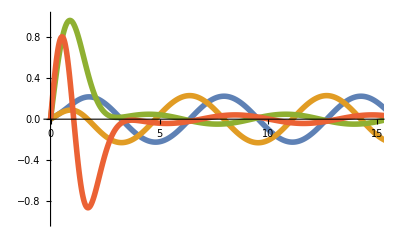

```mathematica
PlotScattEn50SVD=ListPlot[listPhiScattEn50SVDPlot2,PlotRange->{{0,15},{-1,1}},Joined->True,PlotStyle->{Thickness[0.01]},Ticks->{{0,5,10,15},Automatic}]
```

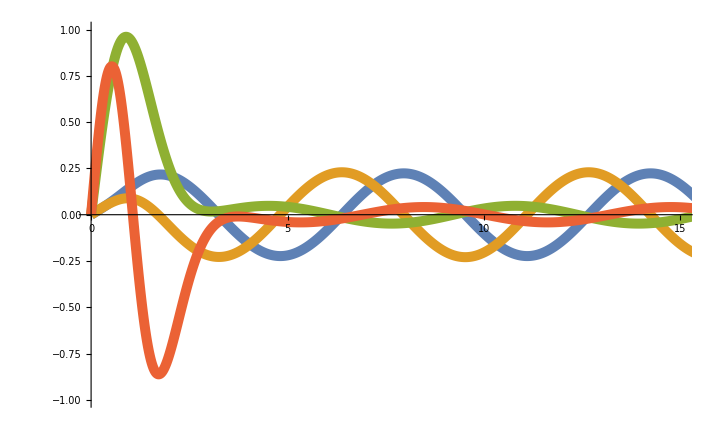

```mathematica
PlotterAdjuster[PlotScattEn50SVD]
```

## PCA Analysis for a varying energy

```mathematica
Length[LHCMatrix]
```

40

```mathematica
Enmin=20;
EnMax=80;
```

```mathematica
EnRange=N[Range[Enmin,EnMax,(EnMax-Enmin)/Length[LHCMatrix]]]
```

{20.,21.5,23.,24.5,26.,27.5,29.,30.5,32.,33.5,35.,36.5,38.,39.5,41.,42.5,44.,45.5,47.,48.5,50.,51.5,53.,54.5,56.,57.5,59.,60.5,62.,63.5,65.,66.5,68.,69.5,71.,72.5,74.,75.5,77.,78.5,80.}

```mathematica
TPSc=TraininPointsMakerScatt[LHCMatrix];
```

```mathematica
TrainingPointsScattEnChange=Table[{TPSc[[i]][[1]],TPSc[[i]][[2]],Sqrt[EnRange[[i]]*2*mu]},{i,1,Length[TPSc]}];
```

```mathematica
ScatFuncsForPlot=BasisConstructionScatt[TrainingPointsScattEnChange];
```

```mathematica
SolsDisplayVaryEn=Table[{xList[[i]],ScatFuncsForPlot[[j*4]][[i]]},{j,1,10},{i,1,1500}];
```

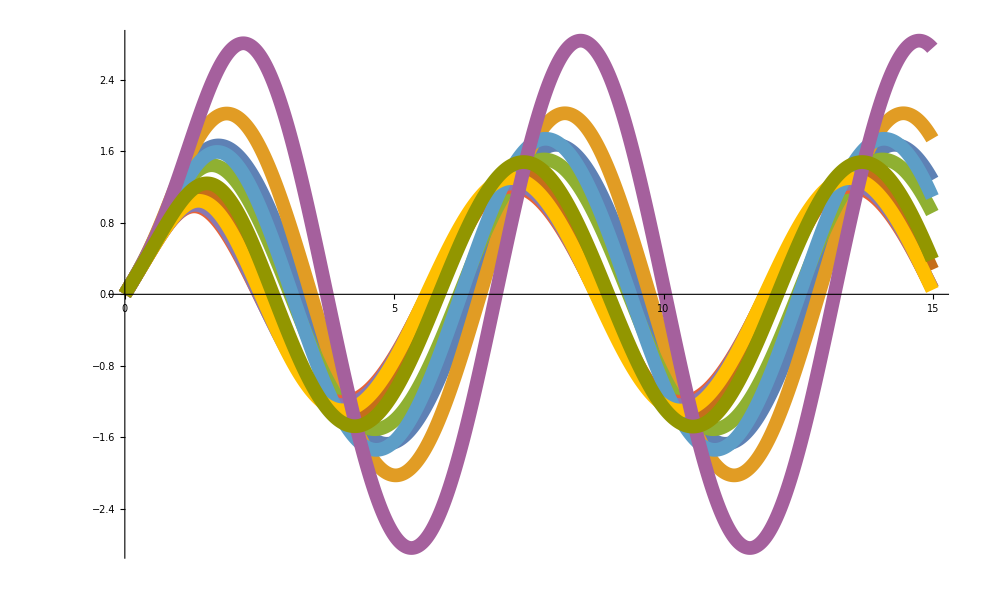

```mathematica
PlotScattEn=ListPlot[SolsDisplayVaryEn,Joined->True,PlotStyle->{Thickness[0.01]},Ticks->{{0,5,10,15},Automatic}]
```

```mathematica
1
```

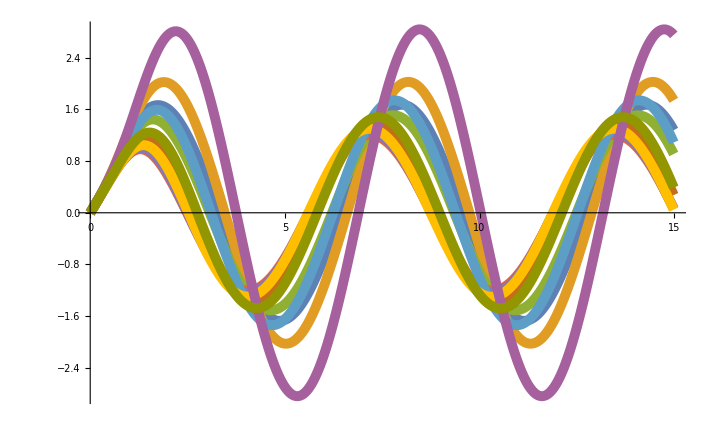

```mathematica
PlotterAdjuster[PlotScattEn]
```

```mathematica
listPhiScattEnChange=BasisConstructionScatt[TrainingPointsScattEnChange];
```

```mathematica
{uScaEn, σScaEn, vScaEn} = SingularValueDecomposition[listPhiScattEnChange,MaxSVDValue];
```

```mathematica
SVDValsScaEn=Table[σScaEn[[i]][[i]]/σScaEn[[1]][[1]],{i,1,Length[σScaEn]}]
```

{1.,0.540208,0.0177044,0.00540696,0.00269172,0.00055628,0.00012348,0.0000244221,9.58557×10^-6,2.43032×10^-6,8.7374×10^-7,5.02474×10^-7,1.70247×10^-7,3.21464×10^-8,8.49829×10^-9}

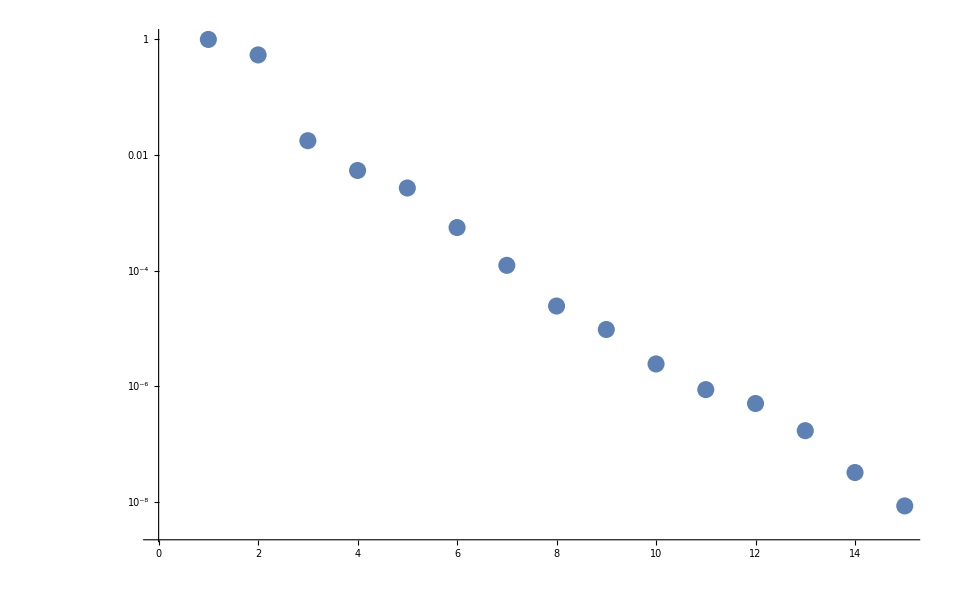

```mathematica
ListLogPlot[SVDValsScaEn]
```

```mathematica
listPhiScattEnSVDPlot=Table[{xList[[j]],10*Transpose[vScaEn][[i]][[j]]},{i,1,4},{j,1,Length[xList]}];
```

```mathematica
listPhiScattEnSVDPlot2={Transpose[{Transpose[listPhiScattEnSVDPlot[[1]]][[1]],Transpose[listPhiScattEnSVDPlot[[1]]][[2]]}],Transpose[{Transpose[listPhiScattEnSVDPlot[[2]]][[1]],-Transpose[listPhiScattEnSVDPlot[[2]]][[2]]}],listPhiScattEnSVDPlot[[3]],listPhiScattEnSVDPlot[[4]]};
```

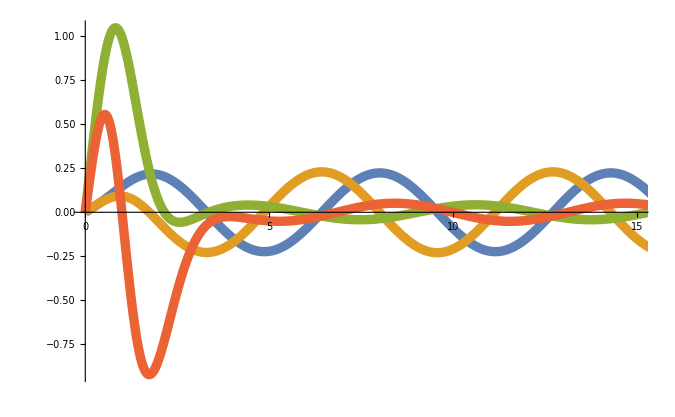

```mathematica
PlotScattEnSVD=ListPlot[listPhiScattEnSVDPlot2,PlotRange->{{0,15},All},Joined->True,PlotStyle->{Thickness[0.01]},Ticks->{{0,5,10,15},Automatic}]
```

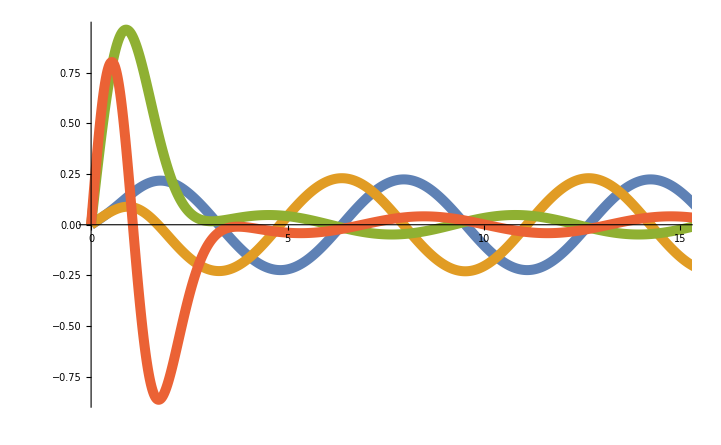

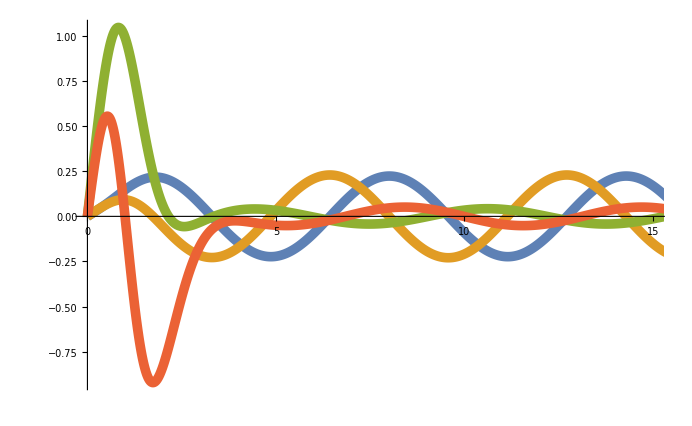

```mathematica
PlotterAdjuster[PlotScattEnSVD]
```

## DFT results

```mathematica
DFTUnNorm=Transpose[{{70.6572775515359,70.6294935180383,70.6367212394498,70.6240221112995,70.5647333053309,70.6207033838854,70.6176005857928,70.5612024536601,70.6123676947656,70.6077193896857,70.6430137864726,70.6393199768787,70.6286823568508},{2.48327567019517,3.17198971261128,3.11128410313841,3.40361077737187,4.31262888388489,3.32231831395313,3.48493969799559,4.42914143981567,3.46441383857391,3.61481668330908,2.95037434098258,3.0520077737624,3.27960747409104},{1.15522022122846,1.16615374572539,0.841190155233973,0.780875322232099,1.29201844601843,1.24872717853892,0.957644205661879,1.00363247619966,1.32068951585988,1.10949715805954,0.894169718130104,0.831767783920773,0.888832608696163},{0.188207100287568,0.187295362051265,0.207761991885192,0.168645811774246,0.522774212677906,0.3043968816842,0.25852820723423,0.64686410502608,0.318830666768988,0.480020580550821,0.209825677584894,0.263185586880148,0.173370364962462},{0.087500594074581,0.126788530637325,0.14254011193409,0.150157045431284,0.219097004241274,0.146533156506933,0.153588299221286,0.222090298410572,0.1962849341857,0.136943121820037,0.117422135987037,0.08567029044688,0.109954730245609},{0.067498258087344,0.040870388782576,0.044966882656436,0.041247108906058,0.153604553190113,0.06858601675883,0.042510873041488,0.133224509821786,0.07991205208105,0.046919886218418,0.048151862470793,0.053952855930635,0.027218438941324},{0.016111448273934,0.018040642768136,0.017592442905063,0.020563278063282,0.070796671156101,0.015241935264672,0.015876944077336,0.07173416514201,0.020163863348719,0.02313877005816,0.013716636836218,0.016667172823701,0.021425056998628},{0.005377448080833,0.007088834279973,0.008805022123394,0.006724002154132,0.019186357807027,0.006616554324824,0.009872116844444,0.036264336156827,0.012040213623296,0.011613370268911,0.004933809039602,0.008723620889689,0.005251904410881},{0.003116864702978,0.00290291306762,0.005197605338043,0.002832121990444,0.006576463657534,0.004683307072982,0.003541066185791,0.011516023941568,0.004246775760522,0.00511635392731,0.002519259492024,0.003386679881947,0.001673096237275},{0.00200951198555,0.00135053277349,0.001881289209374,0.001358546211978,0.00341540993539,0.001662504409594,0.001990664225879,0.005255463301431,0.002649144099413,0.002506297071478,0.001447064739783,0.001088461066133,0.001381705561213},{0.000744598079388,0.000739242577499,0.00067536837227,0.000590037278602,0.002508127343378,0.000669590750037,0.00089697506946,0.00238623209057,0.000971358581829,0.001068334559056,0.000679354767109,0.000727658774267,0.000578093170659},{0.000274612918794,0.00051085830757,0.000305474424584,0.000242519997007,0.001213792080122,0.000509088959521,0.000358909302383,0.001513874207137,0.000360855095976,0.000627626192923,0.000382755494247,0.000213676180924,0.000312441430942},{0.000159962085538,0.000171682208019,0.000102100578979,0.000128667776857,0.000482701243564,0.000172065047501,0.000144512153111,0.000998459031418,0.000289287333007,0.000233517681692,0.000113657538459,0.000116773237466,0.000120499541678},{0.0000687024585195979,0.000103008572377,0.0000671301251062248,0.0000751022084605386,0.000219828374381,0.000126242826413,0.000119625404799,0.000269198229253,0.000160527701328,0.000112016073946,0.0000408965219264451,0.0000563309195337143,0.0000598497687900112},{0.0000294786211791341,0.0000401719921563399,0.000033352053989301,0.0000319601183057054,0.000101972933068,0.000060879822225321,0.00003108671373777,0.000132355434384,0.0000735023724081454,0.0000526286626965505,0.0000216398215326439,0.0000313878959958346,0.0000314852417807724},{0.0000166149903241371,0.0000210476696035476,0.0000249387848614344,0.0000198966840710135,0.0000508675980249337,0.0000254417304480739,0.0000246458993220672,0.0000712105687610638,0.0000369949729860546,0.0000275940377632843,0.0000144027210547592,0.0000205175184953575,0.0000125149569466535},{9.60522164174867*^-6,0.0000112630637339891,0.000016160470557496,8.86695868219634*^-6,0.000026968353003872,0.0000162409974318294,8.72091936068249*^-6,0.000043290097752855,0.0000133996725618925,0.0000100742339542788,7.22897417726324*^-6,0.0000139552232711961,9.68277370268755*^-6},{3.51615635452607*^-6,6.13090539635582*^-6,7.21158193299267*^-6,4.42530227041393*^-6,0.0000101385461982945,5.80252641237794*^-6,6.19704413254324*^-6,0.0000166167368689669,0.0000106695909874209,4.56063156060522*^-6,5.23168144451071*^-6,8.85178275334893*^-6,5.07951615792303*^-6},{2.21517560816671*^-6,2.09286036501754*^-6,4.09227807417783*^-6,2.17890886083078*^-6,7.69052080986937*^-6,2.62802726275786*^-6,2.24374545630402*^-6,9.3711761499393*^-6,2.25949637689334*^-6,2.53515554967295*^-6,1.8363354177566*^-6,2.36271175131104*^-6,2.23943772736574*^-6},{1.09207494597651*^-6,1.74323767856954*^-6,1.26569448191266*^-6,9.84742350228813*^-7,4.63596838983166*^-6,1.52436833123355*^-6,1.53837785239028*^-6,3.28022662756579*^-6,1.81665328291254*^-6,1.35590228319759*^-6,7.5614294123998*^-7,1.16790260892569*^-6,1.14698306241974*^-6},{4.69305501880459*^-7,5.60778162128875*^-7,6.071413345032*^-7,4.58257023759312*^-7,1.54885021481401*^-6,8.92398109407798*^-7,5.53308002584918*^-7,1.94858071925804*^-6,1.1287356171344*^-6,8.95504646363826*^-7,3.61652179956187*^-7,4.50267438409406*^-7,3.67162866448905*^-7},{2.59416265872217*^-7,3.41170043236971*^-7,3.03012894514579*^-7,2.15651500647969*^-7,8.66552610397452*^-7,3.01628218570458*^-7,3.49647749508716*^-7,1.38858708984762*^-6,5.08469527829401*^-7,4.12259982982238*^-7,1.76434597984958*^-7,2.07810460986518*^-7,2.10219625370355*^-7},{1.633756956797*^-7,1.62034938731289*^-7,1.37668666351423*^-7,8.8147570554947*^-8,3.63737515681231*^-7,1.7875836622866*^-7,1.66614689192843*^-7,3.74872553010676*^-7,2.36097939064334*^-7,2.30196830132462*^-7,9.39262866297582*^-8,9.75929498743993*^-8,8.57425192411956*^-8},{9.28963118727619*^-8,7.3879222646394*^-8,7.0952359367638*^-8,6.58857745461143*^-8,2.14936807653811*^-7,8.23070307711639*^-8,1.54303285745066*^-7,2.59684438405303*^-7,1.71067158801377*^-7,1.18969641969938*^-7,4.41188391070388*^-8,5.11633583600691*^-8,5.01994885095089*^-8},{3.93879151114099*^-8,5.92261392515774*^-8,3.09922244032562*^-8,3.72006092017204*^-8,1.02747320281783*^-7,4.59516671643631*^-8,4.7558511628078*^-8,1.49434162791157*^-7,5.51484665972089*^-8,5.21017014125995*^-8,3.65526141584699*^-8,2.15575050660259*^-8,2.44459322618585*^-8},{2.19629552814058*^-8,2.27262859275726*^-8,1.0688931994055*^-8,8.95985914955092*^-9,5.55441538573599*^-8,2.19123530054543*^-8,1.92786995511938*^-8,1.23674688053297*^-7,2.56893711814315*^-8,2.28815015911627*^-8,2.454106990595*^-8,1.48485289145603*^-8,1.10719429262069*^-8},{1.50087656256925*^-8,9.95946107375745*^-9,7.80116142790596*^-9,5.5190472356295*^-9,3.85745863672461*^-8,9.89211702014562*^-9,9.04567604013452*^-9,5.5161748285665*^-8,1.57707385393216*^-8,9.08251240528134*^-9,1.7362478686652*^-8,6.47065462433705*^-9,6.67378905718234*^-9},{9.10605921502619*^-9,4.32939031011522*^-9,3.28627351566886*^-9,3.16568114068362*^-9,2.75370038509271*^-8,7.07752147643664*^-9,3.49506995075997*^-9,3.94379620766009*^-8,6.59435607809189*^-9,4.05234755264786*^-9,8.81550713216308*^-9,3.2689259839466*^-9,4.0992099497588*^-9},{3.20512097528566*^-9,3.33111826695849*^-9,2.14512794303415*^-9,1.83855394721379*^-9,1.22890248015187*^-8,5.56512180371392*^-9,2.50418544156046*^-9,1.7838446101875*^-8,3.54163248258214*^-9,2.2321240169864*^-9,3.24263995153734*^-9,2.91876439668447*^-9,3.31882198994171*^-9},{2.87145754489092*^-9,2.46896740890126*^-9,8.58108243787894*^-10,1.05046745559233*^-9,7.80487187362168*^-9,3.33868274774431*^-9,1.25868551074781*^-9,9.6795100673849*^-9,1.55631376865685*^-9,1.3006685473375*^-9,1.95763604595457*^-9,1.85460625521689*^-9,1.51679407801258*^-9},{1.46403039601234*^-9,1.60712505814341*^-9,5.89899275643403*^-10,6.8206581333359*^-10,4.48862959309452*^-9,1.62729205866981*^-9,6.30962794064973*^-10,3.38001424487002*^-9,9.53343474898403*^-10,5.74622823686412*^-10,9.8379823291036*^-10,1.20296650752254*^-9,1.28009161013555*^-9},{9.89248419566031*^-10,7.05468268032597*^-10,3.46899133370171*^-10,3.25134931458896*^-10,2.30104183491017*^-9,5.71536498692359*^-10,3.29829034617963*^-10,2.34870848124226*^-9,3.5128849177298*^-10,2.91212758221031*^-10,7.15318441393659*^-10,5.7085231215057*^-10,5.83834496023733*^-10},{7.70011757565392*^-10,3.41852501857981*^-10,1.9566145522067*^-10,2.6863059526879*^-10,1.2621593761186*^-9,4.03680126768184*^-10,2.86795511364434*^-10,1.18993018177605*^-9,2.47738974229988*^-10,2.13456029418085*^-10,3.91973130050159*^-10,2.27586648460545*^-10,2.18460492104234*^-10},{4.28266541758208*^-10,1.46171365726515*^-10,1.81480600221884*^-10,1.53638179668129*^-10,6.78571878499493*^-10,1.69585987778758*^-10,1.41336424323005*^-10,1.00618841780078*^-9,1.85949840993092*^-10,7.87336536817063*^-11,3.51576361319743*^-10,1.46391578380192*^-10,1.28749186578168*^-10},{3.31552033861225*^-10,5.98550266246044*^-11,7.12835409704705*^-11,5.01439623182427*^-11,5.35263136530019*^-10,8.05273402408367*^-11,6.62185481491128*^-11,5.63833970411948*^-10,1.51142010865333*^-10,5.40381196557314*^-11,1.15063877089424*^-10,5.43797543790878*^-11,4.78448057820378*^-11},{1.31006373252901*^-10,5.26495175609453*^-11,3.27887282305441*^-11,2.821095513406*^-11,3.79888024604096*^-10,6.14526666497978*^-11,3.62676408123536*^-11,4.5924004558166*^-10,5.27892376426634*^-11,3.30919477543546*^-11,9.37558803854599*^-11,4.45470111703757*^-11,3.9810238122566*^-11},{5.84454544411274*^-11,3.59424908584542*^-11,2.13969216491826*^-11,1.49244035210643*^-11,1.6234009141885*^-10,3.73362410967224*^-11,1.40366339842464*^-11,2.59767180149129*^-10,2.87991681351631*^-11,1.96488656220666*^-11,6.21261098926376*^-11,1.96337757126117*^-11,2.26936379803576*^-11},{2.85508213225211*^-11,1.48779616655731*^-11,1.08275768750885*^-11,1.41500222689977*^-11,8.68793196842259*^-11,1.95055631114769*^-11,9.79509278804451*^-12,1.18136433906674*^-10,1.14303952091618*^-11,1.58142230381382*^-11,2.53277968573406*^-11,1.27655677735836*^-11,8.75980658906097*^-12},{2.13559056519156*^-11,9.90919922366364*^-12,8.45975309186605*^-12,4.98054908391663*^-12,4.64166844653357*^-11,1.01387286668975*^-11,7.81792740618321*^-12,6.71255532983457*^-11,9.70205530650685*^-12,8.02969762782823*^-12,1.22599922708251*^-11,1.15649299293656*^-11,7.06758168513171*^-12},{1.15823804985554*^-11,5.48324903895899*^-12,4.32699589505719*^-12,3.54347017955689*^-12,2.27633565581597*^-11,7.76869482709425*^-12,2.36967109232143*^-12,2.76122498712643*^-11,5.12381652844012*^-12,3.05271255623117*^-12,8.8777923702388*^-12,9.18755874522458*^-12,5.12920074651966*^-12},{6.16101944556823*^-12,4.42649745730279*^-12,2.7992586948947*^-12,1.74975148946657*^-12,1.85132232158223*^-11,6.08712215832586*^-12,1.240127564057*^-12,1.60869311672662*^-11,1.49127710369471*^-12,1.21117448942703*^-12,6.11914527074089*^-12,6.28772203709141*^-12,3.96909853614138*^-12},{3.17404423786439*^-12,3.1451013165791*^-12,1.14505671549637*^-12,1.01834511102823*^-12,1.00835391206374*^-11,4.45819992035466*^-12,6.09320286066667*^-13,1.44874211912683*^-11,1.21960237190946*^-12,7.91773120862234*^-13,3.60854495193376*^-12,5.3657910466966*^-12,3.05563674790916*^-12},{1.40521685512504*^-12,2.53816572667933*^-12,5.89173726397344*^-13,4.25880850617663*^-13,5.86840212663778*^-12,2.78693668315901*^-12,4.95749756434675*^-13,8.43201342705602*^-12,5.47314170156126*^-13,4.8565706908342*^-13,1.53002197976337*^-12,3.71660826839983*^-12,1.83682457229336*^-12},{9.92473099515639*^-13,1.26116786791764*^-12,3.8139031406813*^-13,2.3250712421574*^-13,3.79579609531946*^-12,2.34830625850332*^-12,1.78743809623753*^-13,3.27025521893299*^-12,4.70454486677496*^-13,4.01269445336162*^-13,6.59096812407224*^-13,1.90582749853737*^-12,1.56589971960765*^-12},{6.9786008224674*^-13,8.3141536207305*^-13,2.3625279653776*^-13,1.91196263611826*^-13,1.84034214601714*^-12,1.0903208137538*^-12,1.41654784778811*^-13,1.21899354206189*^-12,3.2039550684172*^-13,1.24541875721745*^-13,3.59314211339733*^-13,9.37403336331962*^-13,7.10039543216689*^-13},{4.19372542693893*^-13,6.11090361548559*^-13,2.0832782644463*^-13,1.34869590882543*^-13,1.46988495531403*^-12,6.75048259756121*^-13,9.82869731378928*^-14,6.79201756017754*^-13,1.3376501065178*^-13,7.28173195720227*^-14,2.48014995229883*^-13,3.49051678009304*^-13,5.04293716424351*^-13},{1.91759724955974*^-13,3.3348388219942*^-13,9.38431258213971*^-14,7.41594823379626*^-14,8.45620401804484*^-13,3.53514413214565*^-13,8.63011988860177*^-14,2.70477054936334*^-13,6.96830326379866*^-14,6.40313494368544*^-14,2.24755368368718*^-13,2.33718963418639*^-13,3.42382961858424*^-13},{1.32103683296901*^-13,2.4582895990736*^-13,5.22045420847246*^-14,5.02881748173328*^-14,4.0484893698552*^-13,2.23315937569756*^-13,5.97042423031348*^-14,2.35516712670428*^-13,5.13559413714365*^-14,3.13561263128718*^-14,1.3107864255027*^-13,1.84620990013548*^-13,2.81584524628998*^-13},{9.30203211426123*^-14,9.43720725112459*^-14,3.77660978932552*^-14,3.08995688416048*^-14,3.16670722258205*^-13,7.23994855949343*^-14,2.29113369100568*^-14,1.78589800200082*^-13,4.08233752313954*^-14,2.20082954869587*^-14,3.52167097153697*^-14,1.2896258138023*^-13,1.09198553725797*^-13},{5.74654994635999*^-14,4.68092019249636*^-14,2.76950070302024*^-14,2.35870790722831*^-14,1.32531952093614*^-13,1.37342246553902*^-14,1.62992033373406*^-14,5.74172839576863*^-14,2.04424636914522*^-14,1.38852561988979*^-14,3.09560826109319*^-14,5.81133460451097*^-14,3.14576699652093*^-14}}];
```

```mathematica
SVDValsDFT=Transpose[Table[DFTUnNorm[[j]][[i]]/DFTUnNorm[[j]][[1]],{i,1,15},{j,1,Length[DFTUnNorm]}]];
```

```mathematica
SVDValsDFT[[1]]
```

{1.,0.0351454,0.0163496,0.00266366,0.00123838,0.000955291,0.000228022,0.0000761061,0.0000441124,0.0000284403,0.0000105382,3.88655×10^-6,2.26392×10^-6,9.72334×10^-7,4.17206×10^-7}

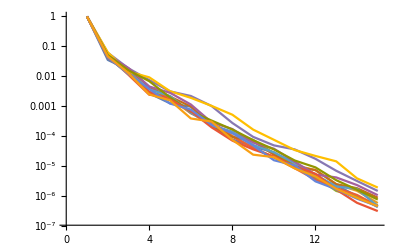

```mathematica
ListLogPlot[SVDValsDFT,Joined->True]
```

```mathematica
Results={SVDValsGP,SVDValsSin,SVDValsSca50,SVDValsScaEn}
```

{{1.,0.151669,0.0475263,0.0111521,0.00346466,0.000987632,0.000386593,0.0000979645,0.0000261418,6.38185×10^-6,3.52778×10^-6,9.78755×10^-7,4.33763×10^-7,1.46656×10^-7,5.84901×10^-8},{1.,0.932583,0.877654,0.820504,0.81858,0.797394,0.594932,0.560805,0.543873,0.532442,0.504846,0.480786,0.443265,0.404685,0.370014},{1.,0.501027,0.0142033,0.00258844,0.000183168,0.0000173313,1.65285×10^-6,1.06313×10^-7,3.76145×10^-8,2.73401×10^-9,2.77957×10^-10,1.64818×10^-11,2.35642×10^-12,1.20269×10^-12,9.92504×10^-14},{1.,0.540208,0.0177044,0.00540696,0.00269172,0.00055628,0.00012348,0.0000244221,9.58557×10^-6,2.43032×10^-6,8.7374×10^-7,5.02474×10^-7,1.70247×10^-7,3.21464×10^-8,8.49829×10^-9}}

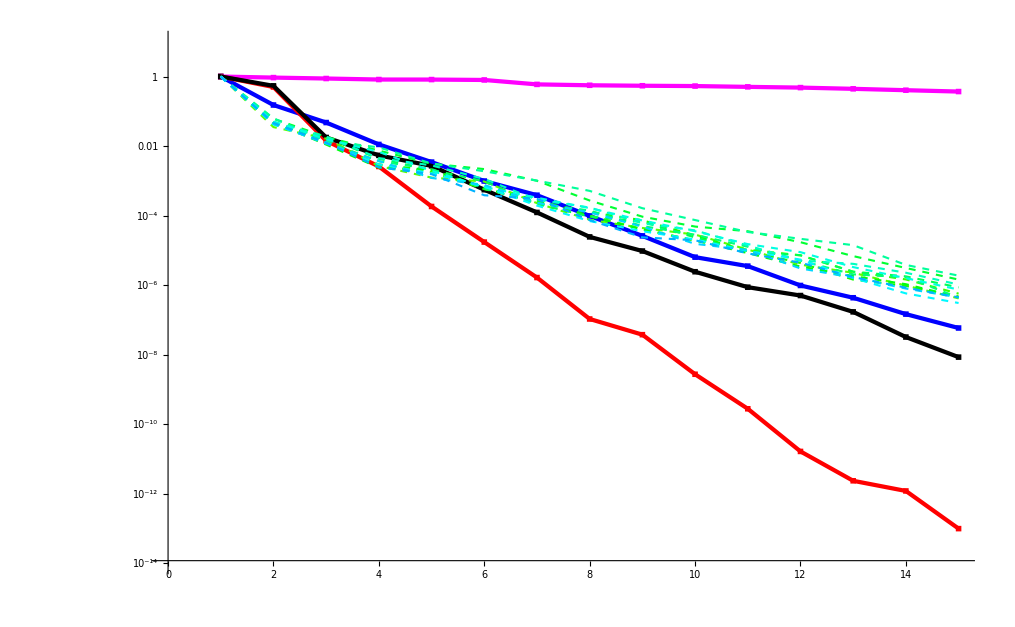

```mathematica
Colors={Blue,Magenta,Red,Black};
Show[ListLogPlot[Results,PlotStyle->Table[{Directive[Colors[[ij]],PointSize[0.02]]},{ij,1,Length[Colors]}],PlotMarkers->{{Graphics[{Rectangle[]}],1/30},{Graphics[{Rectangle[]}],1/30},{Graphics[{Rectangle[]}],1/28},{Graphics[{Rectangle[]}],1/32}},PlotRange->{10^(-14),10},Ticks->{Automatic,{{10^-12,"\*SuperscriptBox[\(10\), \(-12\)]"},{10^-9,"\*SuperscriptBox[\(10\), \(-9\)]"},{10^-6,"\*SuperscriptBox[\(10\), \(-6\)]"},{10^-3,"\*SuperscriptBox[\(10\), \(-3\)]"},{1,"1"}}}],ListLogPlot[Results,PlotStyle->Table[{Directive[Colors[[ij]],Thickness[0.003]]},{ij,1,Length[Colors]}],PlotRange->{{1,16},{10^(-14),50}},Joined->True],ListLogPlot[SVDValsDFT,Joined->True,PlotStyle->Table[{Directive[Hue[ij*0.3/(Length[SVDValsDFT])+0.25],Thickness[0.0015],Dashed]},{ij,1,Length[SVDValsDFT]}]]]
```

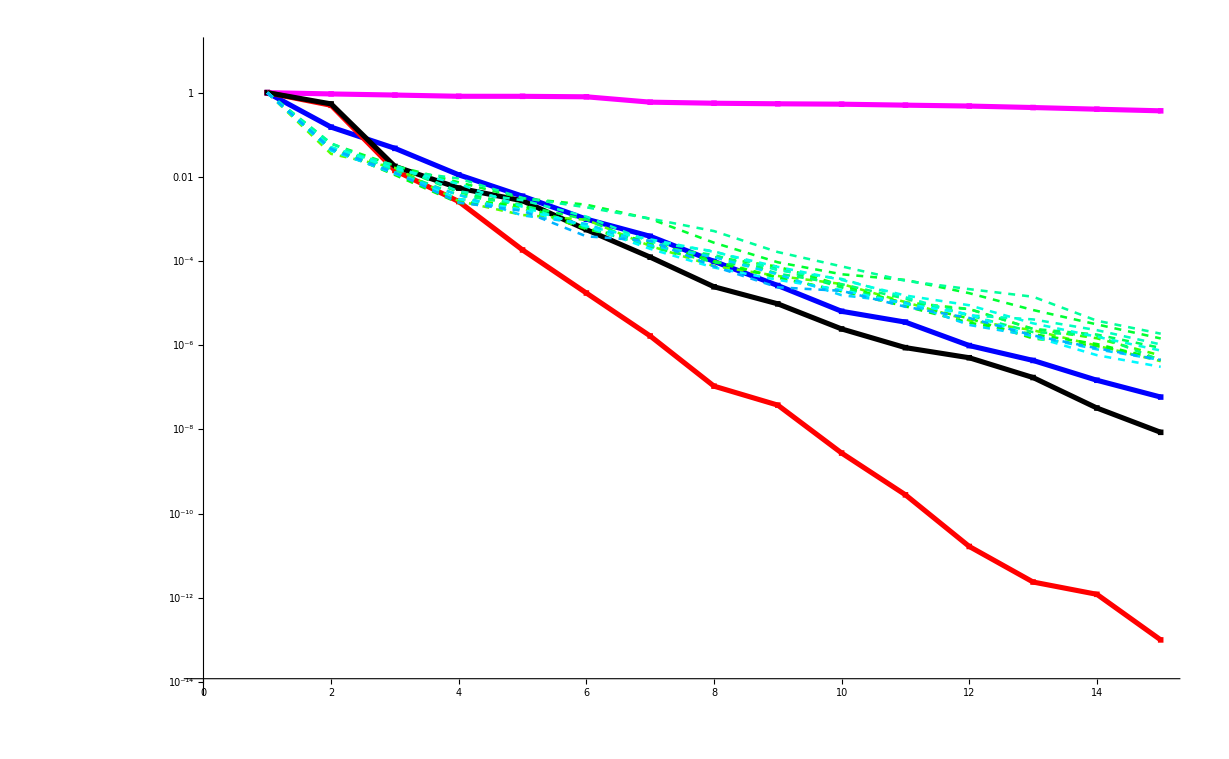

```mathematica
Show[%,PlotLabel->None,LabelStyle->{50,GrayLevel[0]}]
```

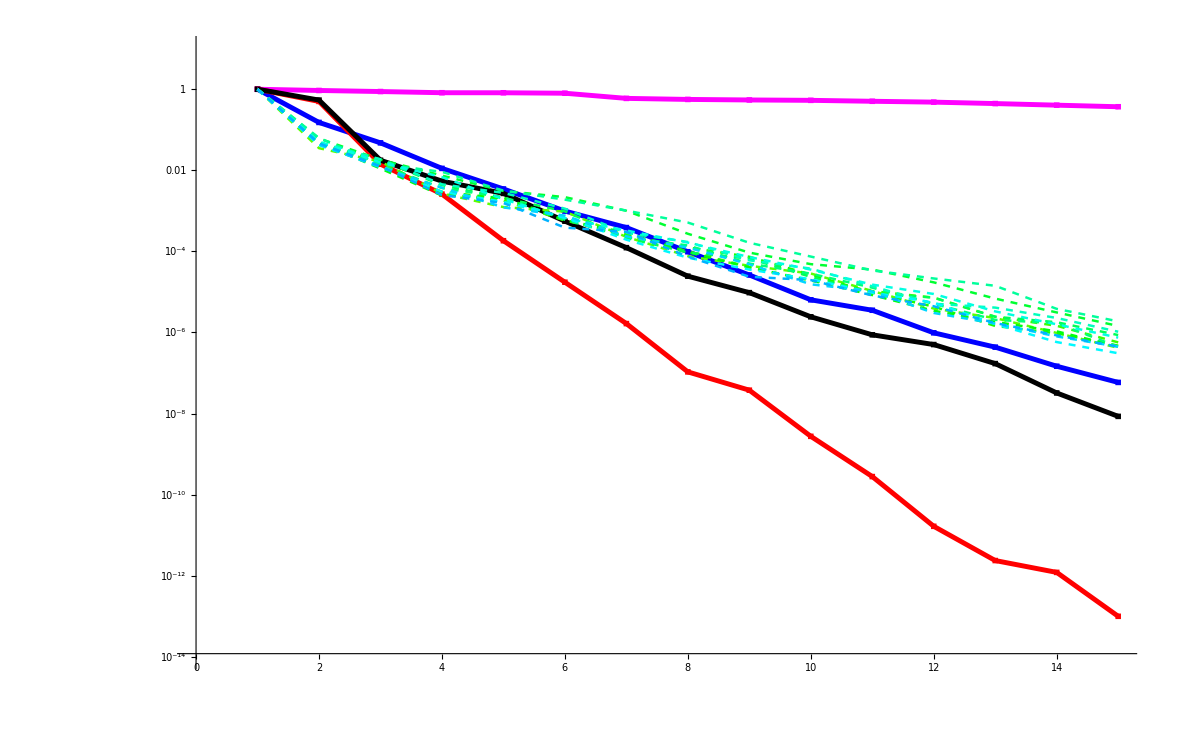

```mathematica
pt=Show[%,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],Method->{"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Exp[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Exp[#1]&)[#1⟦2⟧]}&)}}]
```

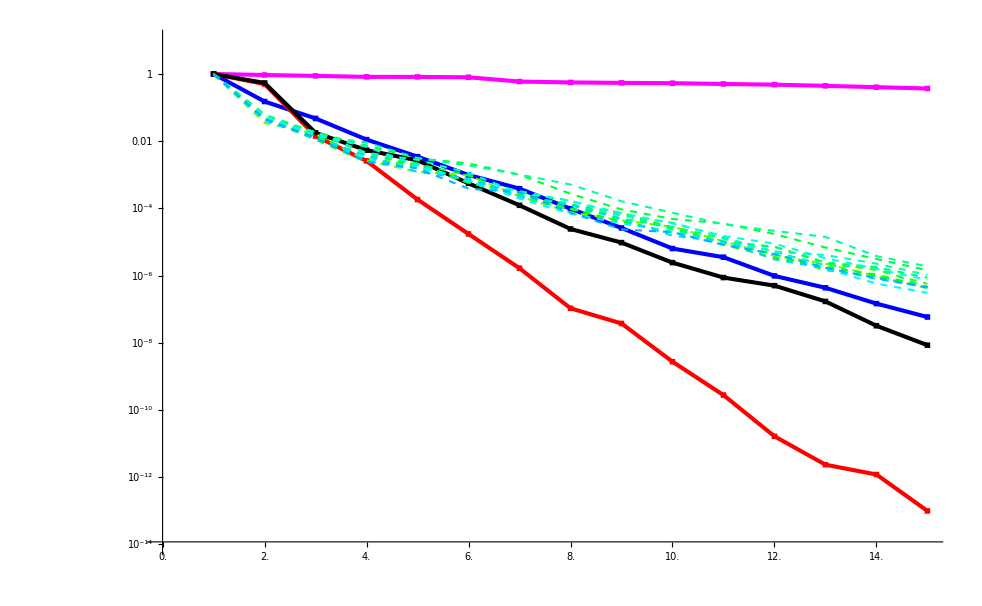

```mathematica
c=3;
tx=Map[MapAt[c #&,#,3]&,Ticks/.AbsoluteOptions[pt,Ticks],{2}];
Show[pt,Ticks->tx]
```

```mathematica
DFTWaveFuncs=Transpose[Import["/home/bell/Documents/Edgard(Work)/NonlinearEVC/DFT_50.csv"]];
```

```mathematica
xsDFT=Table[i*0.01,{i,1,Length[DFTWaveFuncs[[1]]]}];
```

```mathematica
Wfs=Table[{xsDFT[[i]],DFTWaveFuncs[[j*5]][[i]]},{j,1,10},{i,1,Length[xsDFT]}];
```

```mathematica
Wfsraw=Table[DFTWaveFuncs[[j*5]],{j,1,10}];
```

```mathematica
{uCa, σCa, vCa} = SingularValueDecomposition[Wfsraw,4];
```

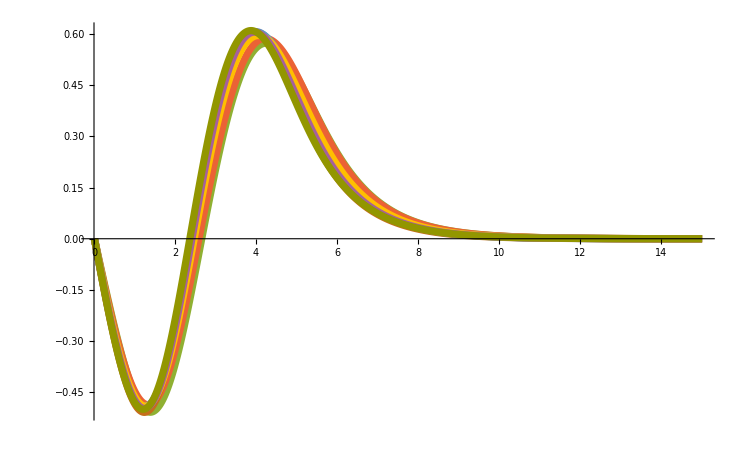

```mathematica
ListPlot[Wfs,Joined->True,PlotStyle->{Thickness[0.007]}]
```

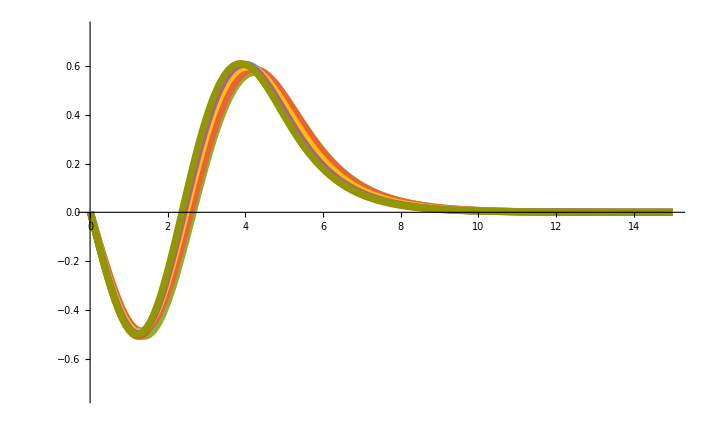

```mathematica
PlotterAdjuster[ListPlot[Wfs,Joined->True,PlotStyle->{Thickness[0.007]},PlotRange->{-0.75,0.75}]]
```

```mathematica
FullListWFSVD=Transpose[vCa];
```

```mathematica
WfsSVD=Table[{xsDFT[[i]],FullListWFSVD[[j]][[i]]},{j,1,4},{i,1,Length[xsDFT]}];
```

```mathematica
nums={-1,-1,-1,1};
```

```mathematica
WfsSVD[[2]]
```

```mathematica
WfsSVD[[1]]
```

```mathematica
WfsSVD2=Table[{WfsSVD[[i]][[j]][[1]],WfsSVD[[i]][[j]][[2]]*nums[[i]]/Sqrt[0.01]},{i,1,4},{j,1,Length[WfsSVD[[1]]]}]
```

{1}
 |  |  |  |

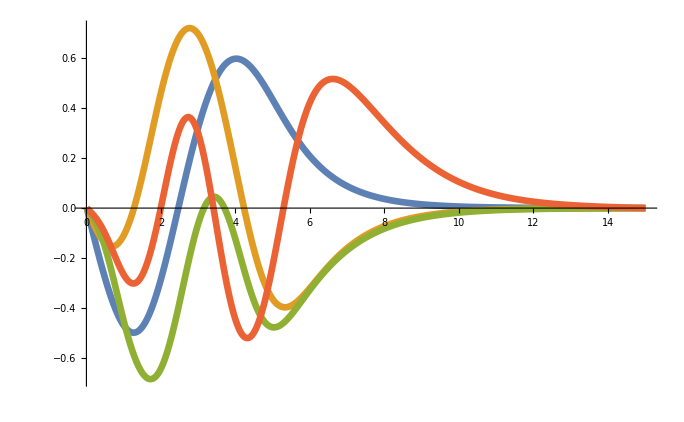

```mathematica
ListPlot[WfsSVD2,Joined->True,PlotStyle->{Thickness[0.007]}]
```

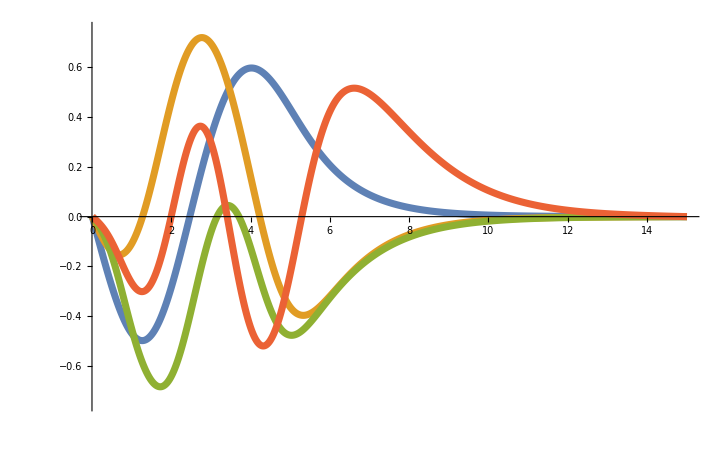

```mathematica
PlotterAdjuster[ListPlot[WfsSVD2,Joined->True,PlotStyle->{Thickness[0.007]},PlotRange->{-0.75,0.75}]]
```